```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LC EOP\\Horizon.xlsx"]
```

```mathematica
data2={{-75.,9.000000000000002},{-70.,9.872340425531915},{-65.,11.568627450980394},{-60.,13.666666666666668},{-55.,15.66},{-50.,17.22},{-45.,17.673076923076923},{-40.,17.796296296296294},{-35.,17.55357142857143},{-30.,18.363636363636363},{-25.,18.88888888888889},{-20.,20.},{-15.,20.816326530612244},{-10.,20.612244897959183},{-5.,21.041666666666668},{0.,20.408163265306122},{5.,20.387755102040817},{10.,19.607843137254903},{15.,19.056603773584907},{20.,18.363636363636363},{25.,17.543859649122805},{30.,16.844827586206897},{35.,16.614035087719298},{40.,16.482142857142858},{45.,16.788461538461537},{50.,16.591836734693874},{55.,15.291666666666668},{60.,13.163265306122447},{65.,11.617021276595745},{70.,10.357142857142856},{75.,9.78125}}
```

{{-75.,9.},{-70.,9.87234},{-65.,11.5686},{-60.,13.6667},{-55.,15.66},{-50.,17.22},{-45.,17.6731},{-40.,17.7963},{-35.,17.5536},{-30.,18.3636},{-25.,18.8889},{-20.,20.},{-15.,20.8163},{-10.,20.6122},{-5.,21.0417},{0.,20.4082},{5.,20.3878},{10.,19.6078},{15.,19.0566},{20.,18.3636},{25.,17.5439},{30.,16.8448},{35.,16.614},{40.,16.4821},{45.,16.7885},{50.,16.5918},{55.,15.2917},{60.,13.1633},{65.,11.617},{70.,10.3571},{75.,9.78125}}

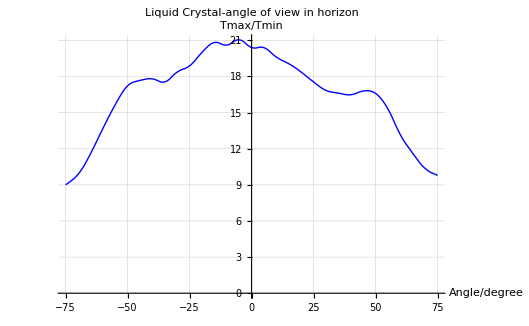

```mathematica
gra1=ListLinePlot[data2,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Angle/degree","Tmax/Tmin"},PlotLabel->"Liquid Crystal-angle of view in horizon",GridLines->Automatic]
```

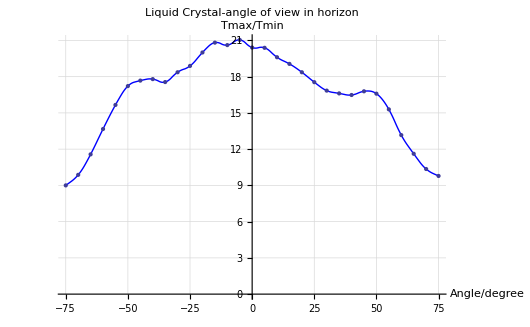

```mathematica
Show[gra1,ListPlot[data2]]
```